```mathematica
SetDirectory[NotebookDirectory[]];
CvData = Import["16_cv.dat","Table"];
MagnetData = Import["16_magnetization.dat","Table"];
SusceptData = Import["16_susceptibility.dat","Table"];
```

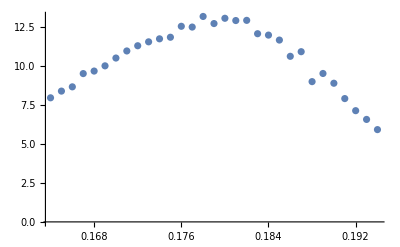

```mathematica
ListPlot[Take[SusceptData,{165,195}], PlotRange->Full]
```

```mathematica
SusceptFit = NonlinearModelFit[Take[SusceptData,{170,195}],A*Exp[-( x-mu)^2/(2 Sigma^2)],{A,Sigma,mu},x];
```

```mathematica
SusceptFit[{"BestFit","ParameterTable"}]
```

{12.9537 ⅇ^(-3166.68 (-0.178613+x)^2), | Estimate | Standard Error | t-Statistic | P-Value
A | 12.9537 | 0.105669 | 122.588 | 6.83315×10^-34
Sigma | 0.0125656 | 0.000278776 | 45.0742 | 6.05216×10^-24
mu | 0.178613 | 0.000175834 | 1015.8 | 5.24183×10^-55}

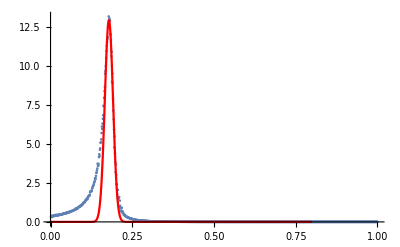

```mathematica
Show[ListPlot[SusceptData, PlotRange->Full],Plot[SusceptFit[x],{x,0,0.8},PlotRange->{{0,0.8},{0,500}}, PlotStyle->Red]]
```

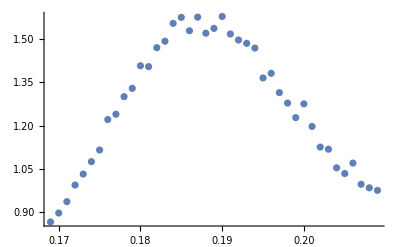

```mathematica
ListPlot[Take[CvData,{170,210}]]
```

```mathematica
CvFit = NonlinearModelFit[Take[CvData,{170,200}],A*Exp[-( x-mu)^2/(2*Sigma^2)],{A,Sigma,mu},x]
```

FittedModel[1.553 ⅇ^(-1827.6 (-«20»+x)^2)]

```mathematica
CvFit[{"BestFit","ParameterTable"}]
```

{1.553 ⅇ^(-1827.6 (-0.187697+x)^2), | Estimate | Standard Error | t-Statistic | P-Value
A | 1.553 | 0.00689795 | 225.139 | 3.65439×10^-47
Sigma | 0.0165403 | 0.000235398 | 70.2653 | 4.92846×10^-33
mu | 0.187697 | 0.000140428 | 1336.61 | 8.0629×10^-69}

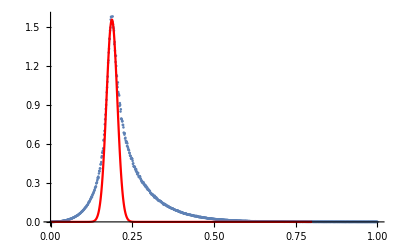

```mathematica
Show[ListPlot[CvData, PlotRange->Full],Plot[CvFit[x],{x,0,0.8},PlotRange->Full,PlotStyle->Red]]
```